```mathematica
MatrixForm[t=Import["data/ASYDATA.DAT","Table",Path -> NotebookDirectory[]]]
```

(H | 0.79
He | 0.49
Li | 2.05
Be | 1.4
B | 1.17
C | 0.91
N | 0.75
O | 0.65
F | 0.57
Ne | 0.51
Na | 2.23
Mg | 1.72
Al | 1.82
Si | 1.46
P | 1.23
S | 1.09
Cl | 0.97
Ar | 0.88
K | 2.77
Ca | 2.23
Sc | 2.09
Ti | 2
V | 1.92
Cr | 1.85
Mn | 1.79
Fe | 1.72
Co | 1.67
Ni | 1.62
Cu | 1.57
Zn | 1.53
Ga | 1.81
As | 1.33
Se | 1.22
Br | 1.12
Kr | 1.03
Rb | 2.98
Sr | 2.45
Y | 2.27
Zr | 2.16
Nb | 2.08
Mo | 2.01
Tc# | 1.95
Rn | 1.89
Rh | 1.83
Pd | 1.79
Ag | 1.75
Cd | 1.71
In | 2
Sn | 1.72
Sb | 1.53
Te | 1.42
I | 1.32
Xe | 1.24
Cs | 3.34
Ba | 2.78
La | 2.74
Ce | 2.7
Dr | 2.67
Nd | 2.64
Pm | 2.62
Sm | 2.59
Eu | 2.56
Gd | 2.54
Tb | 2.51
Dy | 2.49
Ho | 2.47
Er | 2.45
Tm | 2.42
Yb | 2.4
Lu | 2.25
Hf | 2.16
Ta | 2.09
W | 2.02
Re | 1.97
Os | 1.92
Ir | 1.87
Dt | 1.83
Au | 1.79
Hg | 1.76
Tl | 2.08
Pb | 1.81
Bi | 1.63
Po | 1.53
At# | 1.43
Rn | 1.34)

```mathematica
s=Table[t[[All,2]]]
```

{0.79,0.49,2.05,1.4,1.17,0.91,0.75,0.65,0.57,0.51,2.23,1.72,1.82,1.46,1.23,1.09,0.97,0.88,2.77,2.23,2.09,2,1.92,1.85,1.79,1.72,1.67,1.62,1.57,1.53,1.81,1.33,1.22,1.12,1.03,2.98,2.45,2.27,2.16,2.08,2.01,1.95,1.89,1.83,1.79,1.75,1.71,2,1.72,1.53,1.42,1.32,1.24,3.34,2.78,2.74,2.7,2.67,2.64,2.62,2.59,2.56,2.54,2.51,2.49,2.47,2.45,2.42,2.4,2.25,2.16,2.09,2.02,1.97,1.92,1.87,1.83,1.79,1.76,2.08,1.81,1.63,1.53,1.43,1.34}

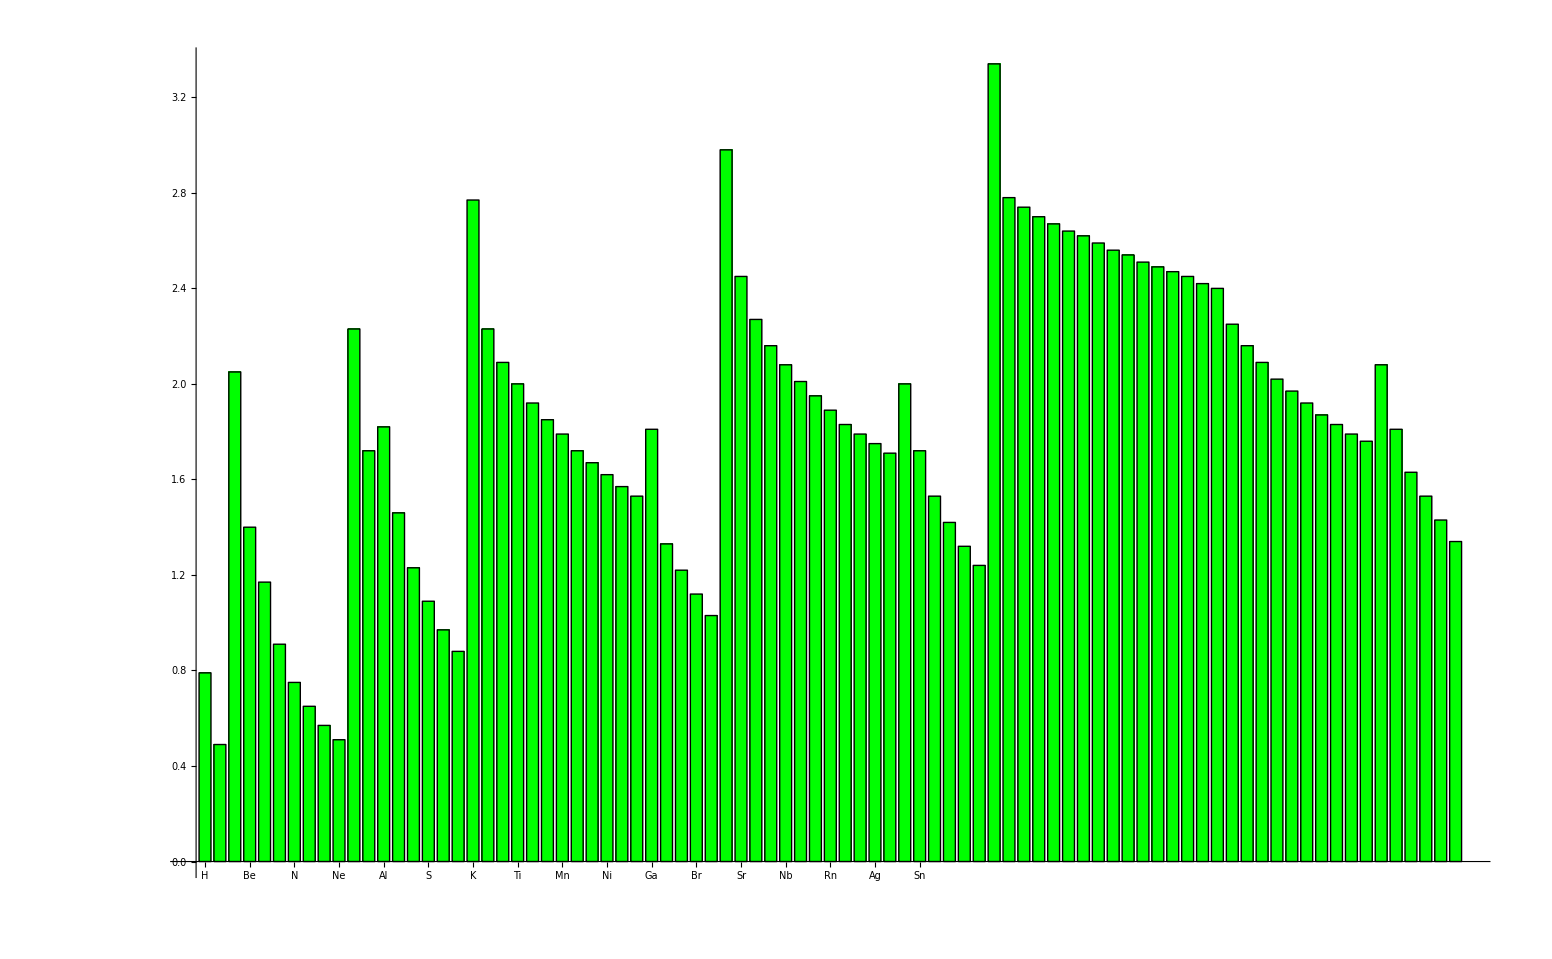

```mathematica
BarChart[s,BarStyle->{RGBColor[0,1,0]},BarLabels->Table[t[[All,1]]]]
```

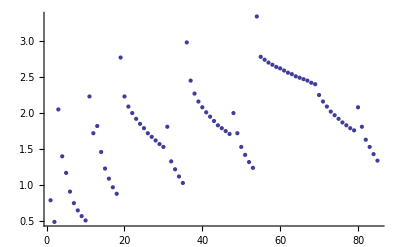

```mathematica
ListPlot[s]
```

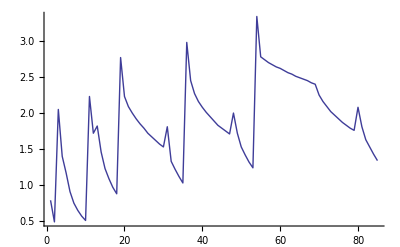

```mathematica
ListPlot[s,Joined->True]
```